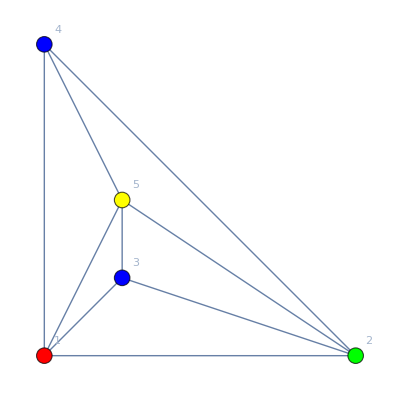
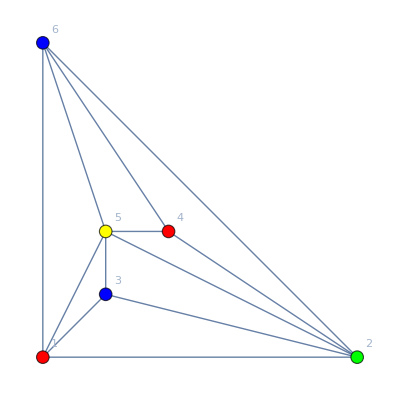
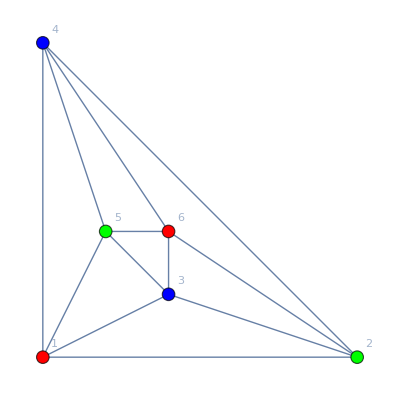
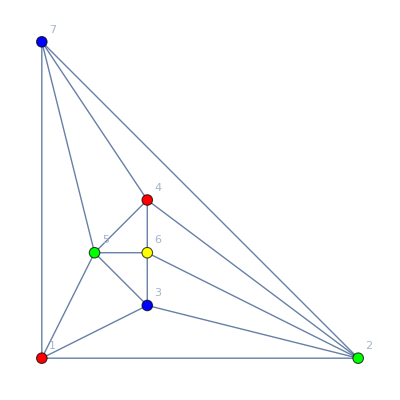
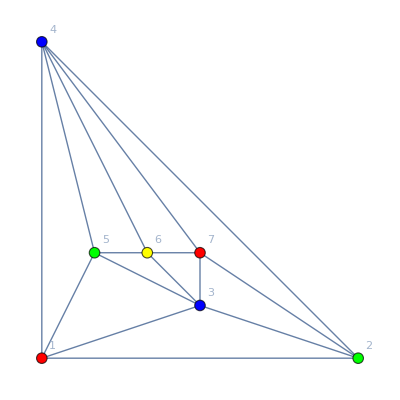
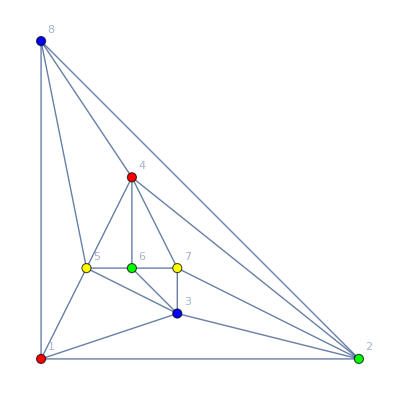
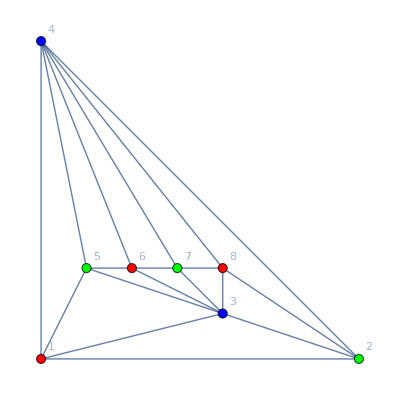
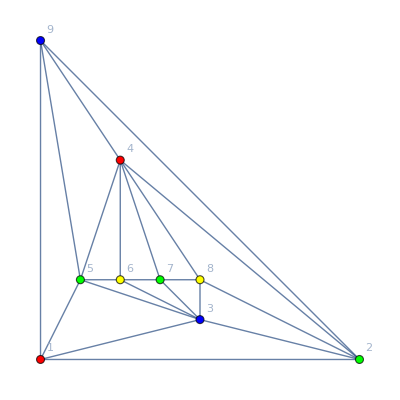
-Graphics- | 1 | -Graphics- | 1
-Graphics- | 4 | -Graphics- | 5
-Graphics- | 5 | -Graphics- | 3
-Graphics- | 12 | -Graphics- | 9
-Graphics- | 21 | -Graphics- | 11
-Graphics- | 44 | -Graphics- | 25
-Graphics- | 85 | -Graphics- | 43
-Graphics- | 172 | -Graphics- | 89
-Graphics- | 341 | -Graphics- | 171
-Graphics- | 684 | -Graphics- | 345
-Graphics- | 1365 | -Graphics- | 683

```mathematica
Monitor[
TableForm[
Table[
With[{g=
Graph[DeleteDuplicates[Join[{1<->2,2<->3,1<->3,1<->4,2<->4,1<->5,max<->2,max<->3},Flatten[Table[{i<->i-1,i<->3,i<->4},{i,5,max}]]]]]},
With[
{h=Rule2[g,1<->4,5<->2]},
{
PaintGraph2First[g,"x1==1&&x2==2&&x3==3",VertexLabels->"Name", GraphLayout->"PlanarEmbedding"], 
ChromaticPolynomial[g,4]/24,
PaintGraph2First[h,"x1==1&&x2==2&&x3==3",VertexLabels->"Name", GraphLayout->"PlanarEmbedding"],
ChromaticPolynomial[h,4]/24
}]
],
{max,5,15}]
],max]
```

```mathematica
Tally[With[{max=7},
Join[{1<->2,2<->3,1<->3,1<->4,2<->4,1<->5,max<->2,max<->3},Flatten[Table[{i<->i-1,i<->3,i<->4},{i,5,max}]]]
]]
```

{{1<->2,1},{2<->3,1},{1<->3,1},{1<->4,1},{2<->4,1},{1<->5,1},{7<->2,1},{7<->3,2},{5<->4,2},{5<->3,1},{6<->5,1},{6<->3,1},{6<->4,1},{7<->6,1},{7<->4,1}}

```mathematica
PaintGraph2First[JacobsThalGraph[15],"x1==1&&x2==2&&x3==3",VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

```mathematica
With[
{g=JacobsThalGraph[10]},
PaintGraph2First[g,"x1==1&&x2==2&&x3==3",VertexLabels->"Name", GraphHighlight->{1<->4},GraphHighlightStyle->"Dashed",GraphLayout->"PlanarEmbedding"]
]
```

-Graphics-

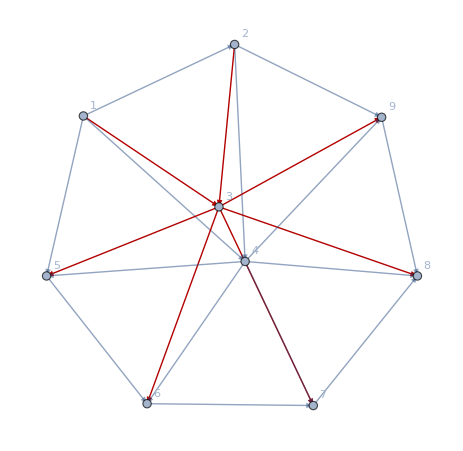

```mathematica
Graph[JacobsThalGraph[5],GraphHighlight->{3<->_,_<->3},EdgeStyle->Opacity[0.5], EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.05}], VertexLabels->"Name"]
```

```mathematica
Table[MaximalPlanarQ[VertexDelete[JacobsThalGraph[i],3]],{i,1,10}]
```

{True,False,False,False,False,False,False,False,False,False}

```mathematica
JacobsThalGraph2[n_]:=With[{max=4+n},Graph[DeleteDuplicates[Join[{1<->2,2<->3,1<->3,1<->4,2<->4,1<->5,max<->2,max<->3},Flatten[Table[{i<->i-1,i<->2,i<->4},{i,5,max}]]]]]]
```

```mathematica
Graph[JacobsThalGraph2[3], GraphLayout->"PlanarEmbedding"]
```

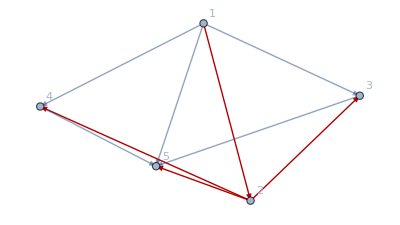
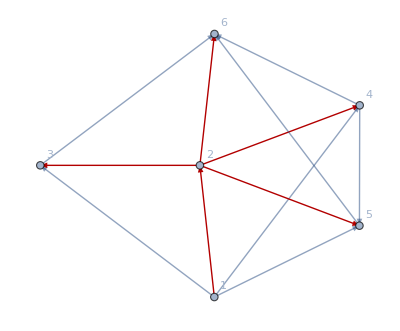
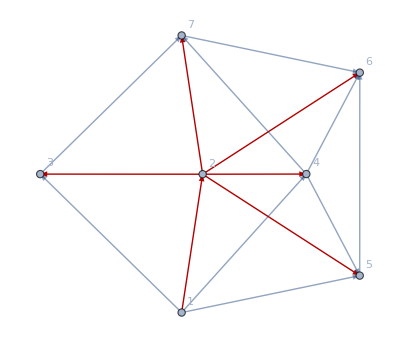
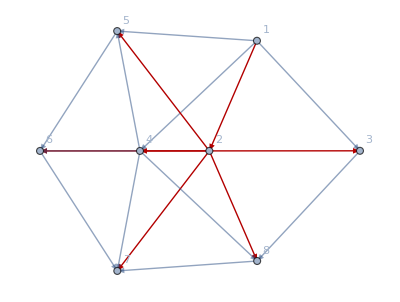
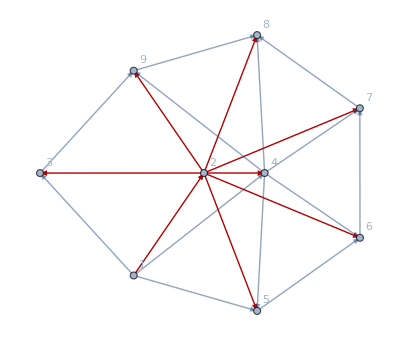
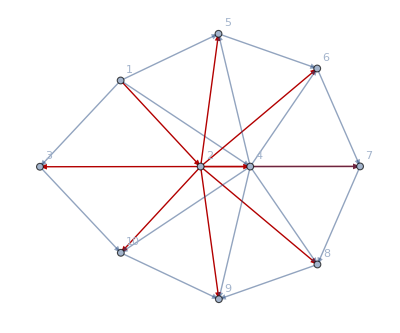
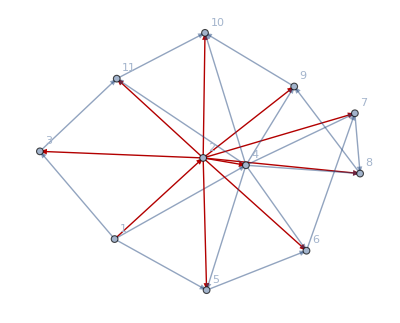
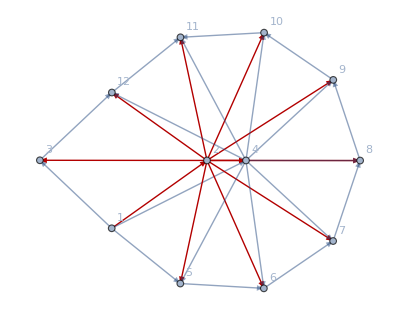

```mathematica
Monitor[Table[
With[{g=JacobsThalGraph2[i]},
Graph[g,GraphHighlight->{2<->_,_<->2}, VertexLabels->"Name",EdgeStyle->Opacity[0.5], EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.05}]]],
{i,1,15}],i]
```

```mathematica
Monitor[Table[
With[{g=JacobsThalGraph[i]},
{VertexCount[g],ChromaticPolynomial[g,4]/24}],
{i,1,30}],i]
```

{{5,1},{6,4},{7,5},{8,12},{9,21},{10,44},{11,85},{12,172},{13,341},{14,684},{15,1365},{16,2732},{17,5461},{18,10924},{19,21845},{20,43692},{21,87381},{22,174764},{23,349525},{24,699052},{25,1398101},{26,2796204},{27,5592405},{28,11184812},{29,22369621},{30,44739244},{31,89478485},{32,178956972},{33,357913941},{34,715827884}}

```mathematica
TableForm[%]
```

5 | 1
6 | 4
7 | 5
8 | 12
9 | 21
10 | 44
11 | 85
12 | 172
13 | 341
14 | 684
15 | 1365
16 | 2732
17 | 5461
18 | 10924
19 | 21845
20 | 43692
21 | 87381
22 | 174764
23 | 349525
24 | 699052
25 | 1398101
26 | 2796204
27 | 5592405
28 | 11184812
29 | 22369621
30 | 44739244
31 | 89478485
32 | 178956972
33 | 357913941
34 | 715827884